```mathematica
f[μ_,x_]:= μ x(1-x)
x[μ_]:= 1-1/μ
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
dfn[μ_,x_,n_]:=D[fn[μ,x,n], x]-1
```

```mathematica
g[μ_,n_,sol]:= D[fn[μ,ξ,n],ξ]/.{ξ->sol}
gμ[μ_,x_,n_]:=D[fn[μ,ξ,n],ξ]
```

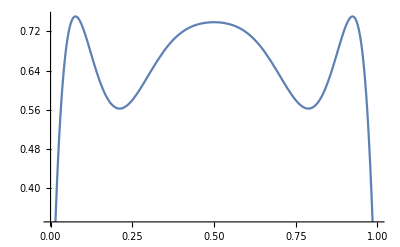

```mathematica
Plot[fn[3,x,3],{x,0,1}]
```

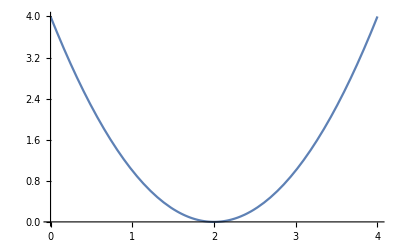

```mathematica
Plot[g[μ,2],{μ,0,4}]
```

```mathematica
Manipulate[Plot[{x,fn[μ,x,8]},{x,0,1}],{μ,0,4}]
```

```mathematica
First/@Flatten[Solve[{fn[μ,x,4]-x==0,μ>3},x,Reals]/.Rule->List/.{x,y_}->y]
```

```mathematica
sol1 = DeleteCases[Drop[First/@Flatten[Solve[{fn[μ,x,4]-x==0,μ>3},x,Reals]/.Rule->List/.{x,y_}->y],1],_Root]
```

{(-1+μ)/μ,(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2),(1+μ)/(2 μ)+1/2 √((-3-2 μ+μ^2)/μ^2)}

```mathematica
NSolve[g[μ,4,(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2)]==1]/@sol1
```

{{{g[μ,4,(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2)]→1.}}[(-1+μ)/μ],{{g[μ,4,(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2)]→1.}}[(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2)],{{g[μ,4,(1+μ)/(2 μ)-1/2 √((-3-2 μ+μ^2)/μ^2)]→1.}}[(1+μ)/(2 μ)+1/2 √((-3-2 μ+μ^2)/μ^2)]}

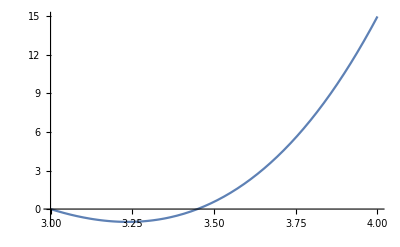

1+√6

```mathematica
x4[μ_]:=(1+μ)/(2 μ)-1/2 Sqrt[(-3-2 μ+μ^2)/μ^2]
g[μ_,n_]:=FullSimplify[D[fn[μ,ξ,n],ξ]/.{ξ->x4[μ]}]
Plot[g[μ,4]-1.,{μ,3,4},PlotRange->Full]
Flatten[Solve[g[μ,4]==1,μ,Reals]/.Rule[μ,x_]->x]//Max
```

```mathematica
punticini[n_]:=DeleteCases[Drop[First/@Flatten[Solve[{fn[μ,x,2^n]-x==0,μ>3},x,Reals]/.Rule->List/.{x,y_}->y],2^(n-1)],_Root]
```

```mathematica
g[μ_,n_]:=FullSimplify[D[fn[μ,ξ,n],ξ]/.With[{μ=1+Sqrt[6]+$MachineEpsilon},FindRoot[{fn[μ,ξ,8]-ξ},{ξ,0.5}]]]
```

```mathematica
Plot[g[μ,8],{μ,1+√6,4}]
```

$Aborted

#### puttana la madonna

```mathematica
Osservazione: si puó automatizzare la ricerca della biforcazione.
Per determinare la biforcazione n-esima si parte da un appropriato valore di μ inferiore a quello di boforcazione (stimato ad occhio) e si confrontano, per un opportunamente grande N, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi siamo arrivati alla biforcazione.
```

```mathematica
f[μ_,x_]:= μ x(1-x)
```

```mathematica
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
```

```mathematica
check[x0_,μ_,nstart_]:= fn[x0,μ,nstart+2^5]-fn[x0,μ,nstart]
```

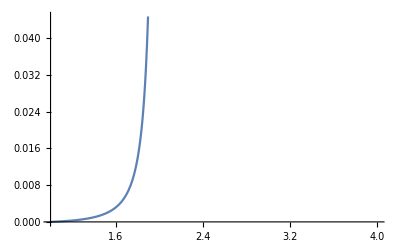

```mathematica
Plot[check[0.5,x,10],{x,1,4}]
```